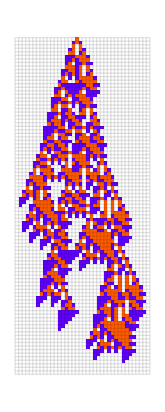

```mathematica
With[{ru={6006804516645,3,1}},GraphicsRow[
{RulePlot[CellularAutomaton[ru],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
MeshStyle->Opacity[.2],ImageSize->280],ArrayPlot[ArrayPad[CellularAutomaton[ru,{{1},0},94],{{0,0},{1,1}}],
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
Mesh->True,MeshStyle->Opacity[.1],ImageSize->{165,Automatic}]},Spacings->40]]
```

### Perturb the organism; what “diseases” can it get?

Can you give other perturbation that will “heal” it?

### Can one evolve a rule that is resistant to perturbation?

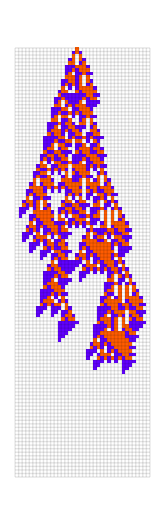

```mathematica
ArrayPlot[ArrayPad[CellularAutomaton[{6006804516645,3,1},{{1},0},120],{{0,0},{1,1}}],
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
Mesh->True,MeshStyle->Opacity[.1],ImageSize->{165,Automatic}]
```

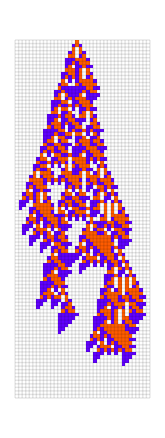

```mathematica
ArrayPlot[ArrayPad[CellularAutomaton[{6006804516645,3,1},{{1},0},100],{{0,0},{1,1}}],
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
Mesh->True,MeshStyle->Opacity[.1],ImageSize->{165,Automatic}]
```

```mathematica
nonzeroRange[list_]:=Flatten[{FirstPosition[list,Except[0],Heads->False],1+Length[list]-FirstPosition[Reverse[list],Except[0],Heads->False]}]
```

Perturbing any number of cells at time tp

```mathematica
perturbedCA[{rn_,k_,r_},init_,tp_,tot_]:=Module[{pat=CellularAutomaton[{rn,k,r},init,tp],row,range},row=Last[pat];range=nonzeroRange[row];Join[pat,CellularAutomaton[{rn,k,r},#,tot-tp]]&/@(Join[Take[row,range[[1]]-1],#,Drop[row,range[[2]]]]&/@Tuples[Complement[Range[0,k-1],{#}]&/@row[[Span@@range]]])]
```

```mathematica
PerturbedCAEvolution[rule, init,perts,ttot ]
```

```mathematica
{t1->ncells,t2->ncells}
```

```mathematica
t1_Integer : t1->1
```

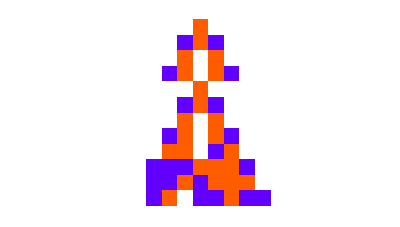
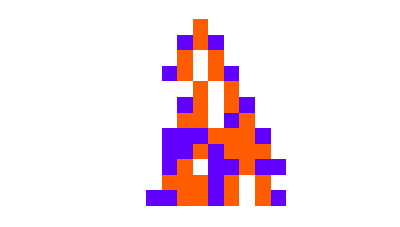
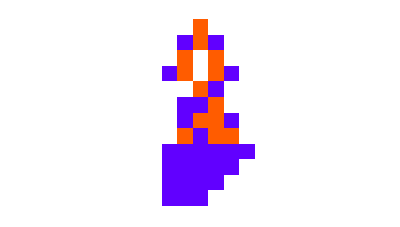
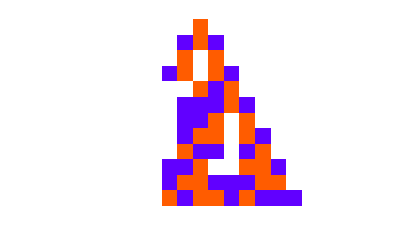
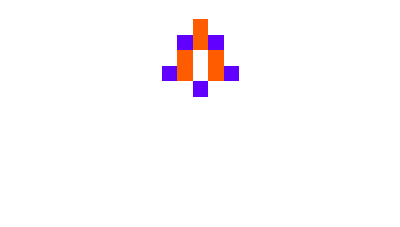
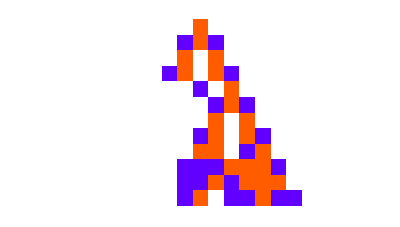
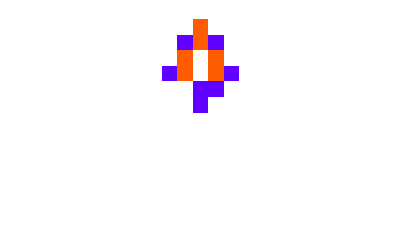
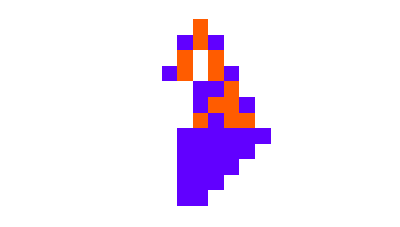

```mathematica
ArrayPlot[#,ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@perturbedCA[{6006804516645,3,1},CenterArray[{1},21],3,10]
```

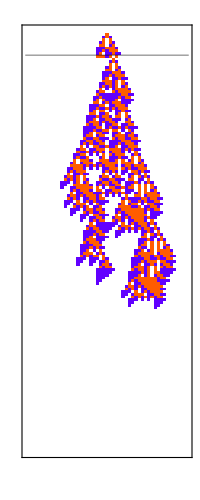
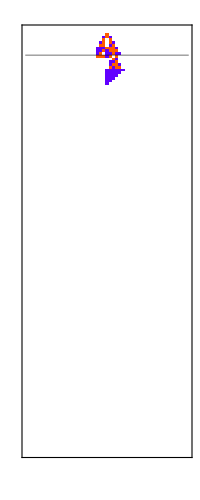
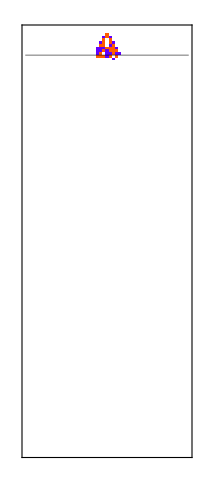
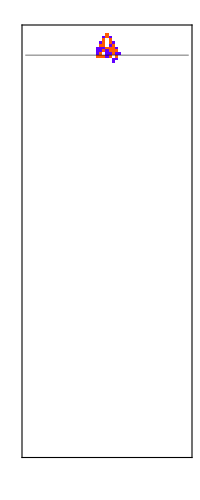
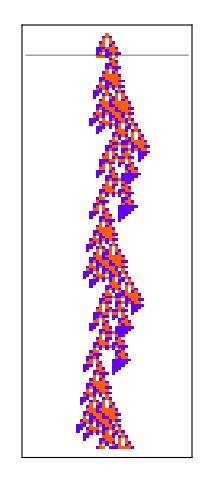
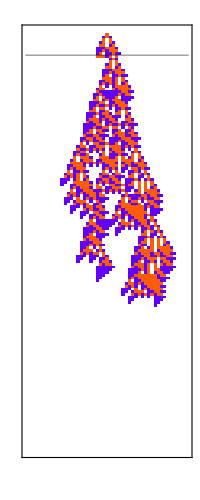
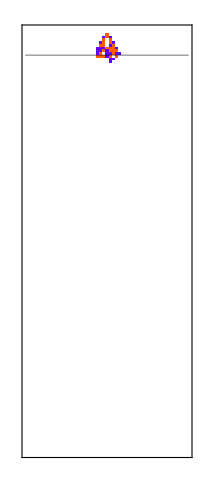
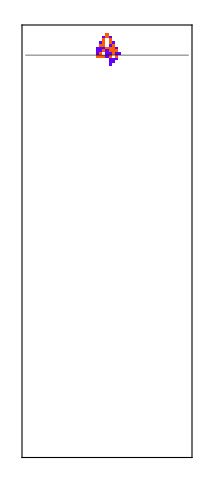
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[#,ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],Mesh->{{8},None},MeshStyle->Opacity[.4],Frame->True]&/@perturbedCA[{6006804516645,3,1},CenterArray[{1},51],8,150]
```

```mathematica
ArrayPlot[#,ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@perturbedCA[{6006804516645,3,1},CenterArray[{1},81],8,200]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
KeySort[Counts[LengthWhile[#,Total[#]>0&]&/@perturbedCA[{6006804516645,3,1},CenterArray[{1},81],8,200]]]
```

<|10→5,11→16,12→11,18→4,19→12,23→1,30→1,89→1,90→1,98→2,99→5,100→10,101→8,102→4,104→1,115→1,116→1,117→4,129→1,202→39|>

```mathematica
Histogram[LengthWhile[#,Total[#]>0&]&/@perturbedCA[{6006804516645,3,1},CenterArray[{1},81],8,200],{1}]
```

-Graphics-

```mathematica
Histogram[Select[LengthWhile[#,Total[#]>0&]&/@perturbedCA[{6006804516645,3,1},CenterArray[{1},81],8,200],#<200&],{1}]
```

-Graphics-

```mathematica
Histogram[Select[LengthWhile[#,Total[#]>0&]&/@perturbedCA[{6006804516645,3,1},CenterArray[{1},81],9,200],#<200&],{1}]
```

-Graphics-

```mathematica
Histogram[Select[LengthWhile[#,Total[#]>0&]&/@perturbedCA[{6006804516645,3,1},CenterArray[{1},81],10,200],#<200&],{1},PlotRange->{{0,200},All},Frame->True,AspectRatio->.3]
```

-Graphics-

```mathematica
Table[Histogram[Select[LengthWhile[#,Total[#]>0&]&/@perturbedCA[{6006804516645,3,1},CenterArray[{1},81],tp,200],#<200&],{1},PlotRange->{{0,200},All},Frame->True,AspectRatio->.3],{tp,4,12}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphicsColumn[%]
```

-Graphics-

```mathematica
Histogram[LengthWhile[#,Total[#]>0&]&/@perturbedCA[{6006804516645,3,1},CenterArray[{1},81],9,200],{1}]
```

-Graphics-

```mathematica
res4=Module[{evo,ru,life,cut=200,deep=5000},
SeedRandom[5053];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep];
evo=Map[{{First[{{"[◼]", "RuleMask"}}@@#],3,1},
Last[#]}&,evo];
{{"[◼]", "AnalyzeEvolution"}}[{3,1},evo]
];
```

```mathematica
GraphicsRow[Map[GraphicsColumn,SplitBy[Values[res4["Plots"]],
Dimensions[#[[1,1]]][[1]]&]]]
```

One-bit perturbation

```mathematica
perturbedCA1[{rn_,k_,r_},init_,tp_,tot_]:=Module[{pat=CellularAutomaton[{rn,k,r},init,tp],row,range},row=Last[pat];range=nonzeroRange[row];Join[pat,CellularAutomaton[{rn,k,r},#,tot-tp]]&/@(Join[Take[row,range[[1]]-1],#,Drop[row,range[[2]]]]&/@Tuples[Complement[Range[0,k-1],{#}]&/@row[[Span@@range]]])]
```

## Roadmap

#### Genetics

Take various evolved systems

#### Disease

Visualize the effect of perturbation at different stages

[ Consider single-cell perturbations + multicell ]   [ Consider perturbations at multiple timesteps ]

```mathematica
PerturbedCAEvolution[rule, init,perts,ttot ]
```

```mathematica
{t1->ncells,t2->ncells}
```

```mathematica
t1_Integer : t1->1
```

[Look at whether these are maximally evolved systems, or not]   [ maximally evolved will probably be more sensitive ]

Measure the effect on lifetime of perturbations   [ histogram ;  change in “life expectancy” (aka mortality curves) ]   [ e.g. plot mean life ; plot quantiles ;   vs. various features of perturbations ]

```mathematica
DistributionChart
```

Try to classify perturbations  (e.g. feature space analysis)  [ dendrograms ]

What is the cascade of perturbations at subsequent steps   (progression of diseases)   ( cascading failures )   [ simple plot:  number of changed cells vs. time after perturbation ]

What effect on longevity do perturbation at different stages have?   [ Could we get a mortality curve that is a Gompertz distribution? ]  [ Materials/GompertzMakeham.nb : Casey Handmer ]

#### Therapy

Is there a subsequent perturbation or pattern of perturbations that heals the system?  [ ~  Maxwell’s demon ]
( “Fundamental problem of medicine is to beat CI” )

[ Is the best way to get back on track just to start again? ]   [ Can longevity work, or is a new generation the only solution? ]

```mathematica
PerturbedCAEvolution[rule, init,{10->1, 15->3},ttot ]
```

Pipeline :  diagnosis [what features of the behavior tell us what therapy to use? ] ⟶ therapy

#### Enhancing health

Can you make perturbations that will make the system live longer?  (But not get a tumor)

#### [Larger genomes]

Evolve for robustness [  i.e. have a fitness function that gets to a lifetime even if there are perturbations ]

How do genome variations affect “diseases”?   [ Simplest case: look at different genomes with identical phenotypes.  How do those different genomes because under perturbation? ]

#### [Perturbations of genomes] [BioEvol2-26-... ]

Lifetime variation purely with perturbations to genome

[ Variations in other properties by varying genomes  :  are there Gaussian distributions?  ]

### Comparison items

ICD-10 tree

https://nvd.nist.gov/vuln/categories

https://cwe.mitre.org/data/definitions/331.html

[ GoL configurations ]

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/VirtualMachine

### Explainability / reductionism

### Medical research practice

[ Clinical trials ]   try various therapies on various perturbations (/ genetic perturbations)  on a sample  ; then: what happens in a larger sample?
[If the outcomes were tightly constrained in the test, what does that imply for deployment?]

[ Theory of diagnosis ]

[ Failure of therapies ]

Can a therapy work on a large part of the population and fail on some ... or work for a while, and then fail

## Large Genomes

```mathematica
AdaptiveCellularAutomaton[   ]
```

```mathematica
Module[
{deep=5000,cut=200,ru,life,evo,data},
SeedRandom[426778];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,5,1},0},deep];
evo=Rest[First/@SplitBy[evo,Last]];
Map[CompoundExpression[
data=CellularAutomaton[
First[#],{{1},0},Last[#]+2],
data=ArrayPad[#,2]&/@data,
ArrayPlot[data,ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,26Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
]
]&,
evo]
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[
{deep=5000,cut=200,ru,life,evo,data},
SeedRandom[426778];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,5,1},0},deep];
evo=Rest[First/@SplitBy[evo,Last]]
]
```

{{{338813178901720135627329000271856784820556640625,5,1},1},{{640285195263131748405462991634643982458245607685885862351291453451330306731699456798625,5,1},4},{{62801543227433624766037456934481288512449274725877769056097139471503677567359663985625,5,1},5},{{314031624667524970437180801133388989224673529256295429543388992017256822839430071861125,5,1},27},{{1252923050335285802813290671965968885765906454811614372199822158175642397664723040454875,5,1},33},{{1256371861244193099469313067576933559634591764041445597708682527816977706216517477954875,5,1},58},{{1256371861244193099469252483059412585927936143287631879726243625562761333249751169361125,5,1},79},{{1256431083589983006971834928370220208815816972451818533496473521161947753652278024829875,5,1},104},{{1350410446345003906488723903645557505039404054930852560712376345698844995721522409595500,5,1},108},{{1350410687055432075783110736188945789973516148215138909616664734138299134000483591236125,5,1},165},{{1162331590923866072930391079791362870699072528566032446828851590915706362947169382251750,5,1},188},{{1151046845155972112853992183229897601703106040477376603259765381161246803029719431079875,5,1},192},{{1339156274684162213092948646627800937220700871548229959440570439263370242341700632251750,5,1},195},{{1057489020317528970214600596701564761213886357722958419624157670121763255819026071704875,5,1},196},{{1057489116614026187998570464862569990124686013269407014002874404476147499307337839283000,5,1},197},{{1997884597271856194373559694640366529203244906483450759703666391950223949178401071704875,5,1},199}}

```mathematica
Counts[Catenate[Partition[#,3,1]&/@CellularAutomaton[{1997884597271856194373559694640366529203244906483450759703666391950223949178401071704875,5,1},{{1},0},200]]]
```

<|{0,0,0}→6653,{0,0,1}→85,{0,1,0}→46,{1,0,0}→153,{0,0,3}→124,{0,3,0}→159,{3,0,0}→131,{0,0,4}→199,{0,4,2}→110,{4,2,0}→66,{2,0,0}→226,{0,0,2}→210,{0,2,1}→83,{2,1,0}→71,{3,0,3}→30,{4,2,2}→85,{2,2,2}→107,{2,2,0}→80,{2,1,1}→61,{1,1,0}→92,{0,3,1}→54,{3,1,0}→47,{1,0,3}→41,{0,4,0}→119,{4,0,1}→40,{0,1,3}→47,{1,3,2}→44,{3,2,0}→51,{0,2,2}→111,{2,2,3}→36,{2,3,4}→30,{3,4,1}→38,{4,1,0}→37,{4,0,2}→50,{0,2,3}→39,{2,3,3}→16,{3,3,0}→22,{2,2,1}→60,{1,1,1}→46,{1,1,4}→21,{1,4,0}→75,{4,0,0}→104,{0,1,1}→43,{1,0,2}→42,{0,2,0}→138,{0,4,1}→39,{1,0,1}→32,{0,1,4}→47,{2,0,3}→51,{0,3,2}→41,{3,2,3}→10,{2,3,0}→34,{3,0,2}→49,{0,4,4}→21,{4,4,2}→23,{2,1,2}→13,{1,2,4}→34,{2,4,0}→53,{2,3,1}→25,{3,1,1}→41,{0,3,4}→16,{4,1,4}→17,{1,4,2}→21,{4,1,2}→33,{1,2,1}→19,{2,2,4}→49,{3,2,1}→17,{1,1,2}→24,{1,2,0}→29,{2,0,2}→33,{4,0,4}→38,{2,0,1}→34,{0,1,2}→22,{2,4,2}→28,{1,2,2}→14,{1,0,4}→24,{4,2,3}→17,{3,0,1}→14,{4,0,3}→29,{2,1,3}→27,{1,3,1}→19,{1,1,3}→14,{1,3,0}→20,{2,0,4}→19,{0,4,3}→7,{4,3,1}→9,{3,2,2}→16,{3,1,4}→7,{1,4,4}→4,{4,4,0}→7,{2,4,3}→4,{4,3,2}→5,{2,4,4}→7,{4,2,1}→14,{2,1,4}→21,{0,2,4}→13,{1,2,3}→5,{3,1,3}→7,{4,3,0}→4,{0,3,3}→4,{3,3,2}→4,{3,4,0}→8,{4,2,4}→6,{2,4,1}→12,{3,0,4}→15,{1,3,3}→8,{3,2,4}→2,{3,4,2}→6,{4,1,1}→6,{1,4,3}→10,{4,3,3}→3,{3,3,1}→4,{1,4,1}→3,{1,3,4}→5,{3,1,2}→9,{2,3,2}→2,{3,3,4}→1,{4,1,3}→1,{3,4,4}→1,{4,4,1}→2,{4,4,3}→1,{4,3,4}→1,{3,3,3}→1|>

```mathematica
Length[%]
```

123

```mathematica
Histogram[Values[Rest[]]]
```

-Graphics-

```mathematica
5^3
```

125

```mathematica
Counts[Catenate[Partition[#,3,1]&/@CellularAutomaton[{1350410446345003906488723903645557505039404054930852560712376345698844995721522409595500,5,1},{{1},0},200]]]
```

<|{0,0,0}→6519,{0,0,1}→24,{0,1,0}→19,{1,0,0}→51,{0,0,3}→40,{0,3,0}→54,{3,0,0}→41,{0,0,4}→62,{0,4,2}→39,{4,2,0}→21,{2,0,0}→69,{0,0,2}→70,{0,2,1}→32,{2,1,0}→24,{3,0,3}→11,{4,2,2}→24,{2,2,2}→35,{2,2,0}→26,{2,1,1}→17,{1,1,0}→26,{0,3,1}→20,{3,1,0}→16,{1,0,3}→12,{0,4,0}→36,{4,0,1}→14,{0,1,3}→13,{1,3,2}→5,{3,2,0}→9,{0,2,2}→33,{2,2,3}→10,{2,3,4}→6,{3,4,1}→2,{4,1,0}→8,{4,0,2}→10,{0,2,3}→12,{2,3,3}→1,{3,3,0}→5,{2,2,1}→15,{1,1,1}→9,{1,1,4}→11,{1,4,0}→24,{4,0,0}→31,{0,1,1}→13,{1,0,2}→18,{0,2,0}→36,{0,4,1}→10,{1,0,1}→7,{0,1,4}→11,{2,0,3}→13,{0,3,2}→10,{3,2,3}→1,{2,3,0}→10,{3,0,2}→12,{0,4,4}→7,{4,4,2}→14,{2,1,2}→8,{1,2,4}→10,{2,4,0}→17,{2,3,1}→8,{3,1,1}→12,{1,3,4}→2,{3,4,0}→7,{4,0,3}→16,{0,3,4}→5,{3,4,4}→2,{4,1,3}→1,{1,3,1}→9,{2,2,4}→16,{3,1,4}→4,{3,2,1}→7,{1,1,2}→8,{1,2,0}→12,{2,0,2}→6,{4,4,0}→3,{2,0,1}→9,{0,1,2}→5,{4,0,4}→15,{1,0,4}→4,{4,2,1}→15,{2,1,4}→16,{0,3,3}→2,{3,0,4}→8,{1,4,3}→2,{4,3,4}→1,{3,4,2}→3,{0,2,4}→4,{2,4,1}→5,{4,1,1}→9,{1,4,2}→5,{4,2,4}→2,{2,4,2}→4,{3,1,2}→4,{2,0,4}→4,{3,4,3}→1,{4,3,2}→4,{3,2,2}→7,{4,1,2}→6,{4,3,1}→3,{3,1,3}→4,{1,3,0}→11,{4,2,3}→3,{2,3,2}→3,{1,2,2}→3,{2,1,3}→8,{1,2,1}→4,{1,3,3}→5,{0,4,3}→3,{3,0,1}→7,{1,4,4}→5,{1,4,1}→6,{1,1,3}→6,{1,2,3}→2,{3,3,2}→2,{2,4,4}→4,{4,4,1}→1,{2,4,3}→2,{3,3,4}→1,{4,4,4}→1|>

```mathematica
Length[%]
```

118

```mathematica
Length[Counts[Catenate[Partition[#,3,1]&/@CellularAutomaton[First@#,{{1},0},200]]]]&/@
```

{0,5,6,62,71,90,116,120,118,121,122,118,122,120,124,123}

```mathematica
ListLinePlot[%]
```

-Graphics-

```mathematica
SeedRandom[235345];Table[{{"[◼]", "TestLifetime"}}[{{"[◼]", "RandomRuleMutation"}}[{1350410446345003906488723903645557505039404054930852560712376345698844995721522409595500,5,1}],200],100]
```

{-∞,-∞,-∞,108,-∞,16,15,15,-∞,-∞,-∞,-∞,108,-∞,-∞,-∞,-∞,-∞,33,138,-∞,73,5,108,-∞,-∞,-∞,21,-∞,-∞,4,108,-∞,-∞,15,-∞,-∞,-∞,-∞,65,-∞,-∞,73,-∞,-∞,-∞,41,-∞,108,-∞,-∞,-∞,-∞,-∞,-∞,73,73,108,-∞,-∞,-∞,-∞,108,39,-∞,-∞,-∞,37,-∞,-∞,-∞,-∞,-∞,-∞,108,-∞,-∞,-∞,108,-∞,108,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,108,-∞,3,-∞,-∞,108,-∞,37,-∞,-∞,17}

```mathematica
ParallelMap[(SeedRandom[235345];Table[{{"[◼]", "TestLifetime"}}[{{"[◼]", "RandomRuleMutation"}}[First@#],300],100])&,]
```

KernelObject::giveup: Timeout for theta.wolfram.com//usr/local/bin/wolfram. Received only 0 of 24 connections.

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{4,4,-∞,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,-∞,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,-∞,4,4,4,4,-∞,4,4,4,4,-∞,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,-∞,4,4,4,4,4,-∞,4,4,4,4,4,4,4,4,4,4,4},{5,5,-∞,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,-∞,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,-∞,5,5,5,5,4,5,5,5,5,-∞,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,-∞,5,-∞,5,5,5,-∞,5,5,5,5,5,5,5,5,5,5,5},{27,-∞,-∞,32,27,7,30,-∞,27,5,25,-∞,41,27,27,27,-∞,27,27,-∞,-∞,27,27,-∞,-∞,27,27,27,27,27,27,39,-∞,27,27,27,27,-∞,27,27,27,27,27,27,23,5,22,27,27,-∞,-∞,-∞,27,27,27,14,-∞,-∞,27,27,4,27,-∞,27,19,-∞,33,27,27,27,27,6,27,-∞,-∞,27,27,27,-∞,-∞,-∞,27,-∞,-∞,-∞,20,22,-∞,-∞,27,27,-∞,27,27,27,27,27,27,27,33},{33,33,-∞,-∞,33,7,58,12,-∞,5,-∞,27,-∞,33,-∞,33,-∞,32,33,-∞,-∞,11,33,30,-∞,33,-∞,33,33,33,30,-∞,-∞,33,33,-∞,33,20,35,-∞,33,33,33,37,-∞,5,22,-∞,33,15,-∞,-∞,33,33,33,-∞,-∞,-∞,-∞,33,4,33,-∞,33,-∞,-∞,-∞,-∞,33,-∞,40,6,33,33,-∞,33,33,33,-∞,33,12,33,-∞,27,-∞,20,16,-∞,-∞,38,33,55,-∞,33,33,33,33,33,33,-∞},{58,-∞,-∞,33,-∞,7,42,-∞,-∞,5,-∞,-∞,-∞,-∞,-∞,58,-∞,58,58,-∞,-∞,11,50,-∞,-∞,58,58,58,58,-∞,63,-∞,-∞,-∞,45,57,-∞,-∞,50,-∞,58,58,58,-∞,58,5,-∞,-∞,58,-∞,-∞,22,93,58,58,-∞,-∞,-∞,-∞,-∞,4,-∞,58,58,-∞,-∞,35,-∞,58,-∞,68,6,-∞,58,27,58,58,58,25,-∞,12,-∞,-∞,52,-∞,20,23,-∞,-∞,-∞,-∞,-∞,-∞,58,58,-∞,58,58,58,35},{-∞,79,-∞,20,64,-∞,-∞,-∞,-∞,5,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,79,-∞,-∞,77,-∞,-∞,-∞,30,-∞,-∞,-∞,79,-∞,-∞,-∞,-∞,-∞,-∞,79,-∞,77,-∞,-∞,-∞,-∞,-∞,-∞,5,16,51,-∞,-∞,-∞,-∞,79,243,-∞,-∞,-∞,58,-∞,-∞,4,-∞,79,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,79,-∞,-∞,-∞,201,-∞,146,-∞,-∞,-∞,-∞,156,94,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{80,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,5,-∞,110,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,30,77,-∞,104,-∞,73,-∞,-∞,-∞,-∞,-∞,-∞,-∞,104,-∞,-∞,-∞,-∞,-∞,-∞,5,16,-∞,-∞,32,-∞,-∞,-∞,-∞,-∞,25,10,-∞,-∞,-∞,4,-∞,104,-∞,-∞,-∞,-∞,-∞,127,-∞,-∞,-∞,62,137,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,46,-∞,-∞,-∞,-∞,-∞,-∞,44,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,26,-∞,-∞,52,-∞,-∞,5,29,51,15,-∞,-∞,-∞,38,89,-∞,108,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,108,-∞,120,-∞,-∞,-∞,-∞,-∞,39,108,-∞,-∞,-∞,30,-∞,-∞,5,16,-∞,29,-∞,-∞,-∞,108,-∞,-∞,-∞,10,-∞,15,26,4,-∞,108,-∞,-∞,-∞,-∞,15,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,119,-∞,-∞,-∞,-∞,-∞},{-∞,-∞,-∞,-∞,-∞,-∞,-∞,52,-∞,5,29,165,15,-∞,-∞,-∞,38,-∞,-∞,-∞,-∞,-∞,-∞,165,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,108,-∞,-∞,63,-∞,165,-∞,-∞,-∞,28,-∞,-∞,5,13,-∞,-∞,-∞,-∞,76,-∞,-∞,-∞,-∞,-∞,-∞,15,-∞,4,-∞,165,-∞,-∞,-∞,165,15,-∞,-∞,105,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,174,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,52,-∞,-∞,-∞,-∞,15,-∞,-∞,-∞,127,165},{-∞,-∞,-∞,25,-∞,-∞,-∞,52,-∞,5,29,188,15,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,188,-∞,-∞,-∞,-∞,166,-∞,-∞,188,-∞,-∞,-∞,-∞,63,-∞,-∞,-∞,-∞,-∞,28,-∞,-∞,5,13,-∞,-∞,-∞,-∞,76,-∞,-∞,-∞,-∞,-∞,-∞,15,-∞,4,-∞,188,-∞,-∞,-∞,188,15,-∞,-∞,111,-∞,209,-∞,-∞,-∞,-∞,-∞,-∞,153,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,52,-∞,-∞,-∞,-∞,15,-∞,70,-∞,127,188},{-∞,-∞,-∞,-∞,67,-∞,-∞,-∞,-∞,5,29,-∞,15,-∞,192,-∞,-∞,192,-∞,-∞,-∞,-∞,-∞,-∞,-∞,175,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,48,-∞,-∞,201,192,46,-∞,28,-∞,-∞,5,13,23,-∞,-∞,-∞,76,-∞,-∞,138,-∞,-∞,-∞,15,-∞,4,-∞,192,-∞,-∞,-∞,-∞,15,-∞,192,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,90,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,15,-∞,-∞,-∞,188,-∞},{-∞,195,-∞,-∞,43,-∞,-∞,-∞,-∞,5,29,-∞,15,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,34,-∞,-∞,-∞,148,-∞,-∞,135,63,-∞,-∞,-∞,-∞,-∞,-∞,-∞,148,-∞,28,-∞,-∞,5,13,-∞,-∞,-∞,-∞,193,-∞,-∞,-∞,-∞,-∞,11,15,-∞,4,-∞,-∞,-∞,-∞,-∞,-∞,15,-∞,-∞,-∞,-∞,-∞,195,-∞,-∞,-∞,66,-∞,195,-∞,28,-∞,-∞,-∞,-∞,-∞,34,-∞,-∞,-∞,-∞,-∞,-∞,15,-∞,-∞,-∞,-∞,-∞},{-∞,196,-∞,-∞,43,-∞,-∞,-∞,-∞,5,52,196,15,-∞,196,38,-∞,-∞,-∞,-∞,-∞,-∞,-∞,196,-∞,127,-∞,-∞,172,-∞,-∞,-∞,-∞,-∞,-∞,143,-∞,-∞,-∞,196,-∞,-∞,28,-∞,-∞,5,13,83,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,11,15,-∞,4,-∞,196,-∞,-∞,-∞,196,15,-∞,196,-∞,-∞,-∞,-∞,-∞,-∞,-∞,66,-∞,196,-∞,28,-∞,-∞,-∞,102,78,-∞,-∞,-∞,-∞,-∞,-∞,-∞,15,32,-∞,-∞,-∞,196},{-∞,-∞,-∞,-∞,81,-∞,-∞,-∞,-∞,5,-∞,-∞,15,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,293,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,48,-∞,-∞,239,-∞,95,-∞,-∞,-∞,-∞,-∞,-∞,-∞,5,13,71,-∞,-∞,-∞,-∞,-∞,49,-∞,-∞,-∞,11,15,-∞,4,-∞,-∞,-∞,-∞,-∞,-∞,15,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,28,-∞,-∞,-∞,-∞,-∞,-∞,-∞,81,114,-∞,-∞,55,-∞,23,-∞,-∞,-∞,-∞},{-∞,199,-∞,25,-∞,-∞,-∞,-∞,-∞,5,-∞,-∞,15,-∞,-∞,75,-∞,-∞,-∞,106,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,276,-∞,-∞,-∞,48,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,76,-∞,-∞,5,13,71,-∞,-∞,-∞,-∞,-∞,-∞,-∞,48,-∞,11,15,-∞,4,-∞,221,-∞,-∞,-∞,200,15,-∞,-∞,94,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,199,-∞,28,-∞,78,-∞,-∞,-∞,-∞,-∞,-∞,114,-∞,-∞,55,144,24,-∞,-∞,203,200}}

```mathematica
Grid[{First@Commonest[DeleteCases[#,-Infinity]],Max[#],Median[DeleteCases[#,-Infinity]]}&/@,Frame->All]
```

1 | 2 | 1
4 | 4 | 4
5 | 5 | 5
27 | 41 | 27
33 | 58 | 33
58 | 93 | 58
79 | 243 | 79
104 | 137 | 54
108 | 120 | 30
165 | 174 | 52
188 | 209 | 63
192 | 201 | 48
15 | 195 | 63/2
196 | 196 | 72
15 | 293 | 38
15 | 276 | 71

```mathematica
ParallelMap[Histogram[DeleteCases[(SeedRandom[235345];Table[{{"[◼]", "TestLifetime"}}[{{"[◼]", "RandomRuleMutation"}}[First@#],300],1000]),-Infinity],{1},PlotRange->All]&,]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### k=10

```mathematica
Module[
{deep=5000,cut=500,ru,life,evo,data},
SeedRandom[426778];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,10,1},0},deep];
evo=Rest[First/@SplitBy[evo,Last]];
Map[CompoundExpression[
data=CellularAutomaton[
First[#],{{1},0},Last[#]+2],
data=ArrayPad[#,2]&/@data,
ArrayPlot[data,ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,26Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
]
]&,
evo]
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[
{deep=5000,cut=500,ru,life,evo,data},
SeedRandom[426778];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,10,1},0},deep];
evo=Rest[First/@SplitBy[evo,Last]];
{Map[CompoundExpression[
data=CellularAutomaton[
First[#],{{1},0},Last[#]+2],
data=ArrayPad[#,2]&/@data,
ArrayPlot[data,ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,26Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
]
]&,
evo],Iconize[evo]}
]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},}

```mathematica
Last/@
```

{1,2,4,6,7,8,46,50,51,71,83,94,95,100,102,123,127,135}

```mathematica
ParallelMap[Histogram[DeleteCases[(SeedRandom[235345];Table[{{"[◼]", "TestLifetime"}}[{{"[◼]", "RandomRuleMutation"}}[First@#],300],1000]),-Infinity],{1},PlotRange->All]&,]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[Counts[Catenate[Partition[#,3,1]&/@CellularAutomaton[First@#,{{1},0},200]]]]&/@
```

{0,0,8,12,14,17,154,157,157,191,263,286,286,299,350,366,336,344}

I.e. there’s enough “noncoding genome” that random mutations probably don’t matter

```mathematica
ParallelMap[Histogram[DeleteCases[(SeedRandom[235345];Table[{{"[◼]", "TestLifetime"}}[Nest[{{"[◼]", "RandomRuleMutation"}},First@#,50],300],1000]),-Infinity],{1},PlotRange->All]&,]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[Histogram[DeleteCases[(SeedRandom[235345];Table[{{"[◼]", "TestLifetime"}}[Nest[{{"[◼]", "RandomRuleMutation"}},First@#,20],300],1000]),-Infinity],{1},PlotRange->All]&,]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[
{deep=10000,cut=2000,ru,life,evo,data},
SeedRandom[426778];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,10,1},0},deep];
evo=Rest[First/@SplitBy[evo,Last]];
{Map[CompoundExpression[
data=CellularAutomaton[
First[#],{{1},0},Last[#]+2],
data=ArrayPad[#,2]&/@data,
ArrayPlot[data,ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,26Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
]
]&,
evo],Iconize[evo]}
]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},}

```mathematica
Last/@First[Last[]]
```

{1,2,4,6,7,8,46,50,51,71,83,94,95,100,102,123,127,135,140,179,185,265,417,458,529,545}

```mathematica
ListLinePlot[%]
```

-Graphics-

## WN Functions

### TODO: Perturbation function, vis function, make memoize function, catalogue lifetime results in disease space, for different stages, locations, intensities, genotypes and phenotypes. Vis results, draw conclusions.

Perturbing any number of cells at time tp

```mathematica
plotca/@ pc
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PerturbedCAEvolution[rule, init,perts,ttot ]:= Module[{pat=CellularAutomaton[rule,init,tp],row,range},row=Last[pat];range=nonzeroRange[row];
topert = test;
Join[pat,CellularAutomaton[rule,#,tot-tp]]&/@(Join[Take[row,range[[1]]-1],#,Drop[row,range[[2]]]]&/@Tuples[Complement[Range[0,rule[[2]]-1],{#}]&/@row[[Span@@range]]])]
```

```mathematica
plotca[ca_, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot}]]:= ArrayPlot[ca, ColorRules -> customstyledata["Colors"],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> OptionValue[ImageSize]
   ]
   
plotrule[rule_, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot}]]:= Module[{digits},
digits = IntegerDigits[rule[[1]], rule[[2]], 27];
plotca[{digits}, ImageSize->OptionValue[ImageSize]]
]

Options[plot] = {"init"->initconditions, "padding"->1, "nsteps"->Automatic};
plot[{ruleidx_, k_, r_}, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot, plot}]] :=  
Module[
{steps = If[SameQ[OptionValue["nsteps"], Automatic], Max[testlifetime[{ruleidx, k, r}, 200], 15], OptionValue["nsteps"]],ca},
  ca = ArrayPad[#, OptionValue["padding"]]& /@ getca[{ruleidx, k, r}, OptionValue["init"], steps];
  ArrayPlot[ca,  ColorRules->OptionValue[ColorRules],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> OptionValue[ImageSize]
   ]]
```

```mathematica
customstyledata = {{"[◼]", "CustomStyleData"}}; analyzeevolution = {{"[◼]", "AnalyzeEvolution"}}
```

```mathematica
nonzeroRange[list_]:=Flatten[{FirstPosition[list,Except[0],Heads->False],1+Length[list]-FirstPosition[Reverse[list],Except[0],Heads->False]}]
```

```mathematica
removeouterzeroes[list_]:=Take[list, nonzeroRange[list]]
```

```mathematica
getdifflocs[pat1_, pat2_] := Position[MapThread[{#1, #2}&,{pat1, pat2}, 2], {x_, y_} /; x != y, 2]
```

```mathematica
towhite[k_, bit_]:= {0}
tored[k_, bit_]:= {1}
toblue[k_, bit_]:= {2}
add1[k_, bit_]:= If[bit == k-1, {0}, {bit + 1}]
sub1[k_, bit_] := If[bit == 0, {k - 1}, {bit -1}]
flipall[k_, bit_]:= Complement[Range[0, k - 1], {bit}]
```

```mathematica
trim[pat_]:= Block[{},
ranges = DeleteCases[nonzeroRange/@ pat, {}];
{left, right} ={Min[ranges[[All, 1]]], Max[ranges[[All, 2]]]};
#[[left -1;;right+1]]&/@ pat
]
```

```mathematica
alignwidth[prepat_, postpat_, row_, pertrow_, overlap_:{-1, 1}]:= Block[{},
l1 = prepat[[overlap[[1]]]];
l2 = postpat[[overlap[[2]]]];
r1 = First@SequencePosition[l1, row]; pad1 = {r1[[1]] - 1, Length[l1]-r1[[2]]};
r2 = First@SequencePosition[l2, pertrow]; pad2 = {r2[[1]] - 1, Length[l2]-r2[[2]]};
If[Length[l1]>=Length[l2], 
padding = pad1 - pad2;
{prepat, ArrayPad[#, padding]&/@ postpat},
padding =  pad2 - pad1;
{ArrayPad[#, padding]&/@ prepat,postpat},
]
]
alignwidth[pat1_, pat2_] := Block[{len1 = Length@pat1[[1]], len2 = Length@pat2[[1]]},
If[len1>= len2, 
diff = len1 - len2;
{pat1, ArrayPad[#, {Ceiling[diff/2], Floor[diff/2]}]&/@pat2},
diff = len2 - len1;
{ArrayPad[#, {Ceiling[diff/2], Floor[diff/2]}]&/@ pat1,pat2}
]
]
```

```mathematica
pertrow[row_, k_, n_]:= Block[{range = nonzeroRange[row],bits,pert, pad},
bits = Take[row, range];
pert = If[n >= Length[bits], flip[k, #]&/@ bits, Join[flip[k, #]&/@ bits[[;;n]], bits[[n+1;;]]]];
pad = Join[row[[;;range[[1]] - 1]], pert, row[[range[[2]]+1;;]]]]
```

```mathematica
pertrow[bits_, k_, n_]:= Block[{pert, pad},
pert = If[n >= Length[bits], flip[k, #]&/@ bits, Join[flip[k, #]&/@ bits[[;;n]], bits[[n+1;;]]]]
]
```

```mathematica
pertrow[row_,idxs_, k_]:= Block[{pert, pad},
ReplacePart[row, #->flip[k, row[[#]]]&/@ idxs]
]
```

```mathematica
pertrow[row_,idxs_, k_]:= Block[{pert, pad},
ReplacePart[row, #->flipall[k, row[[#]]]&/@ idxs]
]
```

```mathematica
sortidxs[idxs_, start_]:=
Which[
start=="Left", idxs,
start=="Right",ReverseSort[idxs],
start=="Center",SortBy[idxs, Abs[Median[idxs] - #]&],
True, idxs
]
```

```mathematica
(*If[ListQ[nperts], pertrow[row, colidxs[[nperts]], rule[[2]]]];*)
```

```mathematica
ClearAll@pertpat
```

```mathematica
Options[pertpat] = {"PerturbationStart"->"Left", "Cut"->1000};
pertpat[{pat_, rule_}, {nrow_,nperts_}, OptionsPattern[pertpat]]:= Module[{},
row = pat[[nrow]];
colidxs =Flatten[Rest[Position[row, Except[0]]]];
sorted = sortidxs[colidxs, OptionValue["PerturbationStart"]];
prow =pertrow[row, sorted[[;;Min[nperts, Length[colidxs]]]], rule[[2]]];
pre = pat[[;;nrow - 1]];
ppat =  CellularAutomaton[rule, prow, OptionValue["Cut"]];
termloc = FirstPosition[ppat, _List?(ContainsOnly[#, {0}]&), {}];
ppatcut = If[termloc == {}, OptionValue["Cut"], Max[Length[pat] - Length[pre], First[termloc]]];
{Join[pat[[;;nrow - 1]], ppat[[;;ppatcut ]]], rule}
]
```

```mathematica
getcoms[list_List]:=Tuples[Replace[list,0:>{0},{1}]]
```

```mathematica
getcoms[{0,{1,2},{0,1},0}]
```

{{0,1,0,0},{0,1,1,0},{0,2,0,0},{0,2,1,0}}

```mathematica
ReplaceAll[{0,{1,2},{0,1},0}, 0->{0}]
```

{{0},{1,2},{{0},1},{0}}

```mathematica
Tuples[{{0},{1,2},{0,1},{0}}]
```

{{0,1,0,0},{0,1,1,0},{0,2,0,0},{0,2,1,0}}

```mathematica
ClearAll@pertpat
```

```mathematica
flipall
```

```mathematica
Options[pertpat] = {"PerturbationStart"->"Left", "Cut"->1000, "PerturbationFunction"->flipall};
pertpat[{pat_, rule_}, {nrow_,nperts_}, OptionsPattern[pertpat]]:= Module[{},
row = pat[[nrow]];
colidxs =Range@@nonzeroRange[row];
sorted = sortidxs[colidxs, OptionValue["PerturbationStart"]];
prow = ReplacePart[row, #->OptionValue["PerturbationFunction"][k, row[[#]]]&/@ sorted[[;;Min[nperts, Length[colidxs]]]]];
allrows = Tuples[Replace[prow,x_Integer:>{x},{1}]];
pre = pat[[;;nrow - 1]];
postlen = OptionValue["Cut"] - Length[pre]+1;
postpats =  CellularAutomaton[rule, #, postlen]&/@ allrows;
termlocs = FirstPosition[#, _List?(ContainsOnly[#, {0}]&), {}]&/@postpats ;
postpatcuts = If[# == {}, postlen, First[#]]&/@ termlocs;
{MapThread[Join[pat[[;;nrow - 1]], #1[[;;#2 ]]]&,{postpats, postpatcuts}], rule}
]
```

```mathematica
showpatdiffs[pat1_, pat2_]:=Block[{},
aligned = alignwidth[pat1, pat2, {1}, {1}, {1, 1}];
locs = getdifflocs@@aligned;
vals = pat2[[#1, #2]]&@@@locs;
rus = MapThread[#1->If[#2 ==0, Black,Replace[#2, customstyledata["Colors"]]]&, {locs, vals}];
highlighted = ReplacePart[aligned[[1]],rus];
ArrayPlot[highlighted, ColorRules->{0->White,_Integer->LightGray}]
]
```

```mathematica
Options[showpatdiffs] = {"Trim"->True};
showpatdiffs[pat1_, pat2_, OptionsPattern[showpatdiffs]]:=Block[{},
{pad1, pad2} = 
If[Length[pat1]>= Length[pat2], 
{pat1, PadRight[pat2,Length[pat1], {pat2[[-1]]}]}, 
{PadRight[pat1,Length[pat2], {pat1[[-1]]}], pat2}]; 
locs = getdifflocs[pad1, pad2];
vals = pad2[[#1, #2]]&@@@locs;
rus = MapThread[#1->If[#2 ==0, -100,-#2]&, {locs, vals}];
highlighted = ReplacePart[pad1,rus];
trimmed = If[OptionValue["Trim"], trim[highlighted], highlighted];
ArrayPlot[trimmed, ColorRules->Join[#[[1]]*-1->#[[2]]&/@ customstyledata["Colors"], { -100->Black,_Integer->LightGray}]]
]
```

```mathematica
ru = {6006804516645,3,1};
pat = CellularAutomaton[ru,{{1}, 0},{100, All}];
```

```mathematica
p = pertpat[{pat, ru}, {10, 1}, "PerturbationStart"->"Center", "Cut"->25];
```

```mathematica
postpatcuts
```

{50,50,50,50}

```mathematica
Length[p[[1, 1]]]
```

26

```mathematica
plotca@ p[[1, 1]]
```

-Graphics-

```mathematica
showpatdiffs[pat, #]&/@ p[[1]]
```

{-Graphics-,-Graphics-}

```mathematica
ps = Table[pertpat[{pat, ru}, {j, i}, "PerturbationStart"->"Right", "Cut"->300], {i,1, 10}, {j,1, 92}];
```

```mathematica
ps = Table[pertpat[{pat, ru}, {10, i}, "PerturbationStart"->"Right", "Cut"->300, "PerturbationFunction"->sub1], {i,1, 10}];
```

```mathematica
ps[[All,1]] // Length
```

3

```mathematica
Length[ps[[1, 1, 1]]]
```

301

```mathematica
Map[showpatdiffs[pat, #, "Trim"->True]&,  ps[[ All, 1]],{2}]
```

{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
showpatdiffs[pat, #, "Trim"->True]&/@ ps[[All, 1]]
```

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},«16»},{{{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},«8»,«291»},{«1»},«7»,{«1»},«16»}},2]; dimensions are 51 and 301.

Function::slotn: Slot number 2 in pad2⟦#1,#2⟧& cannot be filled from (pad2⟦#1,#2⟧&)[2].

Part::pkspec1: The expression #2 cannot be used as a part specification.

Part::take: Cannot take positions 0 through 34 in {0,0,0,0,0,0,0,0,0,0,«41»}.

Part::take: Cannot take positions 0 through 34 in If[«1»].

Part::take: Cannot take positions 0 through 34 in {0,0,0,0,0,0,0,0,0,0,«41»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

ArrayPlot::mat: Argument {{0,0,0,0,0,0,0,0,0,0,«41»}⟦0;;34⟧,«9»,«16»} at position 1 is not a list of lists.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},«16»},{{{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},«8»,«291»},{«1»},«7»,{«1»},«16»}},2]; dimensions are 51 and 301.

Function::slotn: Slot number 2 in pad2⟦#1,#2⟧& cannot be filled from (pad2⟦#1,#2⟧&)[2].

Part::pkspec1: The expression #2 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ArrayPlot::mat: Argument {{0,0,0,0,0,0,0,0,0,0,«41»}⟦0;;34⟧,«9»,«16»} at position 1 is not a list of lists.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},«16»},{{{0,0,0,0,0,0,0,0,0,0,«41»},{0,0,0,0,0,0,0,0,0,0,«41»},«8»,«291»},{«1»},«7»,{«1»},«16»}},2]; dimensions are 51 and 301.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

Function::slotn: Slot number 2 in pad2⟦#1,#2⟧& cannot be filled from (pad2⟦#1,#2⟧&)[2].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

ArrayPlot::mat: Argument {{0,0,0,0,0,0,0,0,0,0,«41»}⟦0;;34⟧,«9»,«16»} at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

$Aborted

```mathematica
PerturbedCAEvolution[rule, init,perts,ttot ]:= Module[{pat=CellularAutomaton[rule,init,tp],row,range},
Fold[pertrow, ]
]
```

```mathematica
{t1->ncells,t2->ncells}
```

```mathematica
t1_Integer : t1->1
```

```mathematica
GraphicsColumn[ParallelTable[Module[{evo,ru,life,cut=200,deep=5000,res},
SeedRandom[5000+i];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep];
evo=Map[{{First[{{"[◼]", "RuleMask"}}@@#],3,1},
Last[#]}&,evo];
res={{"[◼]", "AnalyzeEvolution"}}[{3,1},evo];
out = res;
GraphicsRow[Map[GraphicsColumn,SplitBy[Values[res["Plots"]],
Dimensions[#[[1,1]]][[1]]&]]]
],{i,{16,73,54,60}}]]
```

$Aborted

```mathematica
res4=Module[{evo,ru,life,cut=200,deep=5000},
SeedRandom[5053];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep];
evo=Map[{{First[{{"[◼]", "RuleMask"}}@@#],3,1},
Last[#]}&,evo];
{{"[◼]", "AnalyzeEvolution"}}[{3,1},evo]
];
```

```mathematica
Keys[res4]
```

{Splits,Weights,Differentials,Plots,ChangePositions}

```mathematica
res4["Splits"]
```

<|1→{{0,3,1},1},901→{{54,3,1},2},1087→{{564859112382,3,1},3},1126→{{5648590769046,3,1},4},1155→{{14393166,3,1},6},1171→{{14406288,3,1},6},1195→{{1186220166,3,1},6},1214→{{22106926572,3,1},6},1229→{{1186220166,3,1},6},1303→{{662762785686,3,1},7},1304→{{659275996992,3,1},7},1312→{{376846460511,3,1},8},1316→{{380074964505,3,1},8},1321→{{5464068092322,3,1},8},1337→{{442839211674,3,1},20},1350→{{5527991410125,3,1},24},1352→{{5528077503567,3,1},26},1361→{{5528077680714,3,1},32},1369→{{5527733307108,3,1},32},1377→{{5528077680714,3,1},32},1403→{{5527948540551,3,1},32},1412→{{5621962579215,3,1},32},1420→{{5623121652036,3,1},32},1493→{{5529112396422,3,1},49},1523→{{5529107613453,3,1},125}|>

```mathematica
evo =
```

```mathematica
{{"[◼]", "AnalyzeEvolution"}}[{3, 1}, ]
```

```mathematica
Keys@res4
```

{Splits,Weights,Differentials,Plots,ChangePositions}

```mathematica
res4["ChangePositions"]
```

{{},{{2,4}},{{2,5},{3,5}},{{2,4},{3,5}},{{2,5},{3,4},{3,6},{4,6},{5,6},{5,7}},{{6,5}},{{4,5},{5,5},{5,6}},{{6,7}},{{6,7}},{{3,5},{4,6},{5,5},{5,6},{5,7},{6,5},{6,6},{6,7},{7,4},{7,7}},{{3,4},{4,5},{5,4}},{{5,7},{7,5}},{{4,5},{5,5}},{{3,5},{4,6},{5,7},{6,6},{7,5}},{{4,11},{10,9},{14,9},{16,8},{16,9},{18,6},{18,7}},{{9,10},{11,9},{12,8},{13,7}},{{20,7}},{{9,13},{30,7}},{{4,10},{12,8},{24,6}},{{4,10},{10,8},{12,9},{22,6},{24,7}},{{12,9}},{{3,11},{11,9},{23,7}},{{11,11}},{{3,18},{4,17},{14,14},{15,13},{15,15},{16,16},{18,12},{19,11},{19,13},{19,14},{20,13},{22,10},{22,11},{23,9},{26,9},{29,12},{29,13},{30,12},{34,9},{34,10},{36,8},{37,8},{38,6},{40,7},{40,9}},{{15,27},{18,28},{29,23},{32,21},{32,25},{35,21},{44,20},{46,26},{51,24},{52,22},{55,22},{57,22},{61,24},{63,26},{67,17},{69,26},{71,20},{73,26},{75,22},{76,20},{78,24},{79,19},{81,24},{83,26},{84,18},{86,15},{88,17},{92,17},{96,24},{99,25},{114,20},{117,22},{118,17}}}

```mathematica
customstyledata["Colors"]
```

{0→GrayLevel[1],1→Hue[0.06, 1, 1],2→Hue[0.73, 1, 1],3→Hue[0.14, 0.81, 0.99]}

```mathematica
GraphicsRow[Map[GraphicsColumn,SplitBy[Values[res4["Plots"]],
Dimensions[#[[1,1]]][[1]]&]]]
```

-Graphics-